```mathematica
{t^2,t(t^2-1)}
```

{t^2,t (-1+t^2)}

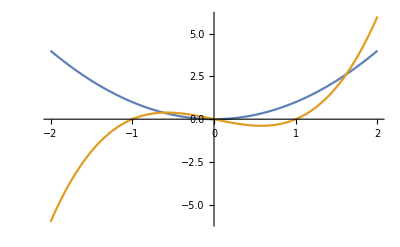

```mathematica
Plot[{t^2,t(t^2-1)},{t,-2,2}]
```

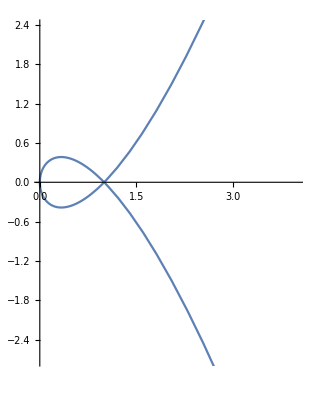

```mathematica
ParametricPlot[{t^2,t(t^2-1)},{t,-2,2}]
```

```mathematica
D[{t^2,t(t^2-1)},t]
```

{2 t,-1+3 t^2}

```mathematica
FullSimplify[Normalize[{t^2,t(t^2-1)}],t∈Reals]
```

{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))}

```mathematica
D[{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))},t]
```

{-((-2 t+4 t^3) Abs[t])/(2 (1-t^2+t^4)^(3/2))+Abs'[t]/(√(1-t^2+t^4)),-(t (-1+t^2) (2 t-4 t^3+6 t^5))/(2 (t^2-t^4+t^6)^(3/2))+(2 t^2)/(√(t^2-t^4+t^6))+(-1+t^2)/(√(t^2-t^4+t^6))}

```mathematica
Norm@{-((-2 t+4 t^3) Abs[t])/(2 (1-t^2+t^4)^(3/2))+Abs'[t]/(√(1-t^2+t^4)),-(t (-1+t^2) (2 t-4 t^3+6 t^5))/(2 (t^2-t^4+t^6)^(3/2))+(2 t^2)/(√(t^2-t^4+t^6))+(-1+t^2)/(√(t^2-t^4+t^6))}
```

√(Abs[-(t (-1+t^2) (2 t-4 t^3+6 t^5))/(2 (t^2-t^4+t^6)^(3/2))+(2 t^2)/(√(t^2-t^4+t^6))+(-1+t^2)/(√(t^2-t^4+t^6))]^2+Abs[-((-2 t+4 t^3) Abs[t])/(2 (1-t^2+t^4)^(3/2))+Abs'[t]/(√(1-t^2+t^4))]^2)

```mathematica
FullSimplify[%7]
```

(√(Abs[t^2+t^4+t^8+t^10]+Abs[(1-t^2+t^4) ((t-2 t^3) Abs[t]+(1-t^2+t^4) Abs'[t])^2]))/(Abs[1-t^2+t^4]^2)

```mathematica
ArcLength[{t^2,t(t^2-1)},{t,a,b}]
```

$Aborted

```mathematica
ArcLength[{t^2,t(t^2-1)},{t,0,1}]
```

∫_0^1 √(4 t^2+(-1+3 t^2)^2)ⅆt

```mathematica
NIntegrate[√(4 t^2+(-1+3 t^2)^2),{t,0,1}]
```

1.3578

```mathematica
FullSimplify[Normalize[{t^2,t(t^2-1)}],t∈Reals]
```

{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))}

```mathematica
NIntegrate[Norm@{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))},{t,0,1}]
```

1.

```mathematica
FinancialData["^VIXY","Name"]
```

Missing[NotAvailable]

```mathematica
FinancialData["VIXY","Name"]
```

ProShares VIX Short-Term Futures ETF

```mathematica
FinancialData["SPXL","Name"]
```

Direxion Daily S&P 500 Bull 3x Shares

```mathematica
With[{
sp=FinancialData["SPXL","Close",All],
vix=FinancialData["VIXY","Close",All]},
Join[
Transpose[{
sp["Dates"][[;;-2]],
Ratios@sp["Values"]
}],
Transpose[{
vix["Dates"][[;;-2]],
Ratios@vix["Values"]
}]
]
]
```

{{Wed 5 Nov 2008 00:00:00GMT-7.,0.847059},5184,{Thu 26 Mar 2020 00:00:00GMT-7.,1.08854}}
 |  |  |  |

```mathematica
GatherBy[Out[17],First]
```

{{{Wed 5 Nov 2008 00:00:00GMT-7.,0.847059}},2864,{{Thu 26 Mar 2020 00:00:00GMT-7.,0.908428},{ | 1,19}}}
 |  |  |  |

```mathematica
{First@First@#,{Last@First@#,Last@Last@#}}&/@Out[18]
```

{{Wed 5 Nov 2008 00:00:00GMT-7.,{0.847059,0.847059}},2864,{Thu 26 Mar 2020 00:00:00GMT-7.,{1}}}
 |  |  |  |

```mathematica
Select[Out[18],Length@#==2&]
```

{{{Tue 4 Jan 2011 00:00:00GMT-7.,1.01544},{Tue 4 Jan 2011 00:00:00GMT-7.,0.978795}},2318,{{ | 1,19},1}}
 |  |  |  |

```mathematica
{First@First@#,{Last@First@#,Last@Last@#}}&/@Out[20]
```

{{Tue 4 Jan 2011 00:00:00GMT-7.,{1.01544,0.978795}},2318,{Thu 26 Mar 2020 00:00:00GMT-7.,{1}}}
 |  |  |  |

```mathematica
rat=Out[21]
```

{{Tue 4 Jan 2011 00:00:00GMT-7.,{1.01544,0.978795}},2318,{Thu 26 Mar 2020 00:00:00GMT-7.,{1}}}
 |  |  |  |

```mathematica
Max/@Last@rat
```

{Thu 26 Mar 2020 00:00:00GMT-7.,1.08854}

```mathematica
Max/@Last/@rat
```

{1.01544,1.00426,1.00205,0.99795,1.01118,1.02776,0.995673,1.01844,1.00905,1.052,0.993684,1.00952,1.01695,1.00065,1.01444,1.00834,1.08373,1.022,1.04686,0.995912,1.00731,1.00776,1.02036,1.01307,1.00488,1.00175,1.01888,1.00758,1.01348,1.01872,1.0099,1.01047,1.12488,1.04418,0.997627,1.03303,1.01926,1.07309,1.00516,1.05167,1.02853,1.02541,1.02617,1.01332,1.05068,1.01875,1.01314,1.0403,1.08993,1.03302,1.01364,1.046,0.991515,1.00852,1.02958,1.00976,1.01275,1.02035,1.02231,0.997965,1.01252,1.00295,1.,1.00787,1.00867,1.01848,0.990954,1.00949,1.00111,1.00258,1.01126,1.02326,1.01567,1.04505,1.01447,0.997846,1.02532,1.01912,1.00971,1.00863,1.02739,1.0226,1.01058,1.02935,1.01192,1.01448,1.02651,1.01973,1.014,1.01343,1.01949,0.997161,1.02907,1.00519,1.01189,1.03344,0.998235,1.01086,1.01496,1.01248,1.03088,1.06322,0.996704,1.00062,1.01628,0.998955,1.01666,1.02083,1.03486,1.01533,1.0381,1.08398,1.0531,1.00823,1.01619,1.04204,1.01049,0.999217,1.04115,1.02357,1.0402,1.02675,1.02817,1.04291,1.00433,1.01544,1.03219,1.01103,1.08322,1.02477,1.00973,1.03629,1.01769,1.02138,1.05011,0.997603,1.04026,1.00358,1.03814,1.02063,1.05916,1.02306,0.982328,0.986052,1.06944,1.0165,1.1967,1.05104,1.14646,1.14324,1.12049,1.1405,1.02112,1.06477,1.02273,1.01996,1.20677,1.05048,1.03043,1.09987,1.04163,1.02061,1.04919,1.08726,1.01197,1.01801,1.01261,1.05043,1.02964,1.083,1.01626,1.09525,1.019,1.02914,1.04281,1.05126,1.01429,1.03381,0.9989,1.05429,1.10091,1.01933,1.06807,1.03571,1.06387,1.02286,1.07329,1.06488,1.0686,1.05731,1.05777,1.01814,1.10214,1.00333,1.02784,0.998046,1.05137,1.10569,1.06223,1.0682,1.01628,1.05458,1.04591,1.06489,1.02902,1.08956,1.01302,1.1061,1.1478,1.04703,1.0553,1.01875,1.01498,1.03794,1.1868,1.02342,1.05804,1.02539,1.01435,1.04782,1.04958,0.995562,1.01248,0.987171,1.04641,1.01302,1.08683,1.0074,1.12484,0.999833,1.,1.03032,1.00098,1.02844,1.04664,1.05033,1.00496,0.994832,1.00381,1.01322,1.00526,0.990375,1.08965,1.0077,1.02869,1.02423,1.00194,1.04296,1.02774,1.01528,1.04438,1.00189,1.01162,0.993167,1.00547,1.02908,1.01653,1.00572,1.02644,1.00727,1.0349,1.01672,1.00086,1.00186,1.00474,1.02697,1.00071,1.00057,1.02934,1.00035,1.02976,1.00625,1.04267,0.998411,1.00891,1.02297,1.04894,1.08556,1.02062,1.03102,1.05726,1.03446,1.00551,1.00089,0.98956,1.01557,1.0352,1.01108,1.00803,0.986647,1.02064,1.00702,0.99671,1.0767,1.02278,1.03061,1.01315,0.997504,1.05591,1.03096,1.01594,1.00644,1.01024,0.989402,0.996391,1.01049,1.01041,1.0406,1.09515,1.00847,0.996207,1.00854,1.02367,1.01734,1.02446,1.02173,1.06066,1.08146,1.02298,1.04276,1.05601,0.995852,1.04494,1.01597,1.00799,1.00298,1.03239,1.01079,1.04295,1.01999,1.00602,1.02265,1.01903,1.00909,1.02121,1.04381,1.00241,1.00969,1.03867,1.00612,1.01281,1.05895,1.05135,1.03264,1.04917,1.06271,1.05419,1.03441,1.00384,1.0081,0.989999,1.03642,1.0675,1.01442,1.08479,0.994364,1.02362,1.06799,0.999711,1.0236,1.08275,1.0334,1.05079,1.03043,1.02728,1.01123,1.0287,0.995612,1.11362,1.01941,1.08388,1.01679,1.02671,0.991748,1.07433,1.00775,1.02058,1.03587,0.989546,0.995611,1.02968,1.00014,1.01006,1.04735,0.994025,1.02004,1.022,1.00884,1.05441,1.06335,1.04284,0.998204,1.049,1.05674,1.0188,1.02981,0.996434,0.978506,1.05852,1.00605,1.0261,1.00314,1.00301,1.00493,0.998326,1.05664,1.00251,1.02256,1.00357,1.00168,1.02645,1.00654,1.02072,1.01704,1.00829,1.01809,1.00363,1.02173,1.01122,0.99809,0.998805,1.06045,1.01298,1.05544,1.00862,1.00832,1.04794,1.03013,0.994356,0.996817,1.00202,0.999044,0.998618,0.995953,1.07654,1.03961,1.02819,1.03167,1.00775,1.00452,1.01162,1.0233,0.998094,1.011,1.04459,0.987507,1.0009,1.01068,1.02494,1.03098,1.01301,0.996595,1.06378,1.00068,1.07801,1.00553,1.009,0.997301,1.01699,1.03628,1.0275,1.0166,1.02307,1.07856,1.00658,1.00292,1.00431,1.00054,1.03326,1.00883,1.01324,1.06254,1.00298,1.00782,1.03595,0.997981,1.02079,1.02225,1.01455,1.01804,1.02278,1.01733,1.00464,1.01196,1.00714,1.0146,1.01819,1.02657,1.01831,1.0062,1.03758,1.03272,1.0557,1.02513,1.06556,0.988946,1.05556,1.00055,1.05094,1.05311,1.07621,1.00869,1.01278,0.998645,0.994043,1.00674,1.02338,1.00094,0.996368,1.00104,1.00042,1.01924,1.00704,1.0155,1.00519,1.00577,1.01607,1.02681,1.01233,1.06449,1.0023,1.03068,1.06855,1.0291,1.00289,0.99683,1.0154,0.999526,1.00541,1.00667,1.00311,0.995514,1.02119,1.08865,1.01629,1.02997,1.13753,1.01948,1.03704,1.0304,1.01553,1.01484,1.02766,1.00426,1.00532,1.01283,1.0101,1.01525,1.00309,1.01662,1.00091,1.05158,1.00086,1.01884,1.02909,1.02208,0.990554,1.02163,1.01016,1.00596,1.00367,1.01395,1.03487,1.01404,1.00371,1.02011,1.0083,1.0391,1.00941,0.992396,1.11604,1.04189,1.11655,1.04211,1.02329,1.0135,1.03317,1.00293,1.01135,1.,1.01828,1.00664,1.04403,1.02607,1.02932,1.00997,1.01387,1.01484,1.0182,1.01014,1.00205,1.03142,1.01435,1.01011,1.02821,1.01543,1.00912,1.00904,1.00796,0.999013,1.01811,1.01624,1.00973,1.03403,1.01435,1.01359,1.04119,1.02768,1.03669,1.00134,1.06324,1.06003,1.044,1.02755,1.02448,1.02187,1.,1.11791,1.00944,1.06147,1.02942,1.02758,1.01814,0.995548,1.02545,1.01388,1.00333,1.03173,1.01744,1.02188,1.00088,1.04169,1.01082,1.01313,1.02805,1.00783,1.01743,1.00537,1.00493,0.995775,1.01179,1.00819,1.00115,1.01247,1.,1.00249,1.03358,1.00501,0.996807,1.0299,1.01233,1.00926,1.01315,0.995277,1.01011,1.01113,1.04939,0.992623,1.02776,1.01473,1.01856,1.02575,1.01026,1.03311,1.08012,1.00964,1.02301,1.01125,1.01349,1.02616,1.00176,1.00861,1.02977,1.02126,1.01041,1.01775,1.00562,1.01753,1.01258,1.03667,0.995167,1.01697,1.01319,0.995372,0.997443,1.01043,1.0415,1.03408,1.02227,1.03175,1.03688,1.02165,1.07795,1.04591,1.00263,1.06483,1.01927,1.01267,1.06096,1.04229,1.02048,1.01835,1.00435,1.01498,1.00574,1.00916,1.01352,1.0053,1.01636,1.0134,0.995112,1.00918,1.01037,0.997015,1.01418,1.03557,1.03962,0.999284,0.999384,1.02321,1.01653,1.01263,1.00063,1.01173,0.990614,1.02334,1.01406,1.00437,1.00401,1.00643,1.01197,1.00822,1.02477,0.99708,1.00804,1.03261,1.00794,1.00534,1.04613,1.00476,1.00189,1.01932,0.995595,1.05222,1.01087,1.0164,1.01565,1.0073,1.01481,1.01298,1.01673,1.01366,1.02033,0.99726,0.992403,1.0184,1.00179,1.00179,1.00734,1.03507,1.03146,1.01645,1.00476,1.00036,1.00959,1.00174,1.0258,1.09151,1.01536,1.01828,1.06767,1.03275,1.07944,1.07177,1.0209,1.03661,1.03928,1.03869,1.00429,1.03299,1.00314,1.01435,1.0161,1.00352,1.06848,1.01691,1.01021,1.01395,1.00016,1.013,1.01612,1.01635,1.05615,1.04467,0.999093,1.00877,1.02127,0.998951,1.01304,1.00061,1.04064,1.02831,1.0275,1.02181,1.019,1.01755,1.00716,1.00203,1.01488,1.0178,0.995155,1.01319,1.0248,1.01951,1.00994,0.99854,1.01974,1.02331,1.01281,1.03265,1.06081,1.03039,1.02408,1.02011,1.03052,1.00416,1.01137,1.01215,1.00441,1.01207,1.00723,1.00969,1.0131,1.01053,0.999256,0.995979,1.00538,1.00645,1.01694,1.00346,1.00407,1.02834,1.00323,0.994762,1.00972,1.01213,1.00989,0.990445,1.02495,1.00782,1.01274,1.01749,0.997301,1.01624,1.00252,1.00503,1.0045,1.00474,1.02121,1.01371,1.01435,0.999867,1.02284,1.04757,1.00951,1.00191,1.0079,1.02204,1.00357,1.01545,0.999345,1.0359,1.01282,1.01305,1.00502,0.999343,1.02012,1.00245,1.01466,1.02044,1.01787,1.01227,1.03641,1.00496,1.01454,1.01748,1.01068,1.09796,1.02966,1.02589,1.01351,1.00913,1.,1.02839,1.00038,0.996339,1.01785,1.08613,1.04748,1.02139,1.07082,1.00444,1.02077,1.03445,1.00894,0.99659,1.0208,1.0126,1.00104,1.02343,1.01513,1.00879,1.00934,0.996276,1.01547,1.00931,1.00705,1.0167,1.00793,1.00694,0.998768,1.00215,1.01451,1.00219,1.02672,1.01168,1.00273,1.02279,1.02517,1.02274,1.00346,1.01527,1.00165,1.03304,1.03838,1.02404,1.07541,1.02365,1.05013,1.01218,1.02166,1.00013,1.03287,1.01622,1.07132,1.05246,1.09207,1.11318,1.10209,1.00692,1.01117,1.02324,1.03799,1.0282,1.05842,1.07836,1.03484,1.02133,0.996717,1.03373,1.01526,1.0197,1.03324,1.01635,0.992686,1.01774,1.01226,1.00238,1.00948,1.00235,1.01239,1.01171,1.00263,1.00199,1.01752,1.02519,1.00565,1.01641,1.00801,0.998208,1.00718,1.02648,1.04171,1.01913,1.01158,1.0034,1.00535,1.03629,1.01223,1.10653,1.06203,1.05187,0.979501,1.04914,1.05863,1.07332,1.01284,1.01392,1.00421,1.0011,1.00904,1.00371,1.02482,1.0814,0.999088,1.07472,1.02167,1.0372,1.0532,1.03906,1.04746,1.02871,1.01788,1.03085,1.03752,1.00692,1.01555,1.04415,1.02547,1.00786,1.04318,1.08467,1.0281,1.10189,1.03568,1.04319,1.02804,1.03104,1.04296,1.00482,1.03162,1.00408,1.02787,1.0135,1.00433,1.00032,0.998167,1.0175,1.00363,1.00818,1.00701,0.996303,0.996206,1.01886,1.02198,0.997242,1.00259,1.04596,1.01234,1.03207,1.02159,1.03885,1.02301,1.0409,0.993425,1.03599,1.00173,1.02671,0.994562,0.99464,1.04611,0.992701,1.00597,1.037,1.02593,0.999412,1.00811,1.02118,1.00061,1.01018,1.01395,1.01528,1.02582,1.00556,1.01409,0.998397,1.03282,1.02683,1.,1.01527,1.00662,1.00742,1.03098,1.00917,1.02758,1.02684,1.03096,1.00962,1.03247,1.01817,1.01143,1.03907,1.02701,0.995736,1.00119,1.03079,1.00335,1.0094,0.998448,1.00236,1.00893,1.00242,1.04026,1.02675,1.01207,1.00556,1.00586,1.01475,1.00882,1.03357,0.992231,1.02126,0.99856,1.03671,1.00941,1.01249,1.04359,1.01749,1.00476,1.03024,1.01079,1.02053,1.0024,1.02124,1.00693,0.999571,1.17056,1.00744,1.02148,1.06405,1.02558,1.01788,1.1007,1.00633,1.03749,1.03301,1.01317,0.999148,1.02154,1.00459,1.00187,0.990817,0.994439,1.01305,1.03404,1.05249,1.03589,1.02103,1.00064,0.998129,0.989821,1.0038,1.01035,1.03828,0.993045,1.03691,1.04638,1.00363,0.99561,1.01113,1.01592,1.01092,1.01926,1.08756,1.1661,1.17878,1.09001,1.11715,1.07281,1.0493,1.0377,1.14198,1.05629,1.00124,1.07312,1.07665,1.02018,1.01614,1.01355,1.00231,1.03909,1.02565,0.992818,1.12235,1.01564,1.05806,0.994573,1.0271,1.02577,1.06998,1.00276,1.05644,1.00811,1.04294,1.05398,1.00992,1.02468,1.0273,1.00125,1.00388,1.05562,1.01788,1.04548,1.01298,1.00232,1.03777,1.06962,1.04966,1.03355,1.0339,0.994336,1.03418,1.01232,1.01622,1.03515,1.02104,1.03298,0.996142,0.998561,1.055,1.00639,1.02199,1.08845,1.06881,1.04552,1.05484,1.0476,1.03558,1.01238,0.994837,1.00451,0.999438,1.00883,0.993636,1.02926,1.03759,1.07327,1.05785,1.02564,1.02984,1.04229,1.01202,1.14996,1.01649,1.02985,1.04269,1.04361,1.08134,1.02751,1.02715,1.03625,1.0172,0.993562,1.03292,1.02923,1.02302,1.06527,1.00669,1.03282,1.10734,1.05166,1.00058,1.02557,1.10336,1.04663,1.09981,1.00421,1.02651,1.01224,1.06174,1.04759,1.04082,1.04162,1.01622,1.07243,1.00043,1.0665,1.01616,1.00961,1.03986,1.04805,1.00873,1.00703,1.06179,1.05943,1.04967,1.04916,0.997692,0.999852,1.04184,1.05098,1.01207,1.03577,1.01563,1.01355,1.07447,1.01283,1.01134,1.01119,1.00277,1.03793,1.01564,1.00212,1.04781,0.996334,1.0147,1.01707,1.01854,1.01156,1.00498,0.998185,1.04894,0.998517,1.0012,1.02847,1.0131,1.00777,1.01938,1.02827,1.05584,1.03197,1.09233,1.00858,1.0139,1.0288,1.02931,1.00081,0.996068,1.02113,1.00952,1.00566,1.01876,1.00046,1.01134,1.00551,1.00468,1.05801,1.0316,1.02339,1.04498,1.01282,1.,1.01115,1.003,1.03526,1.03462,0.999052,1.03593,1.02899,1.04444,1.,1.00485,1.01732,0.996981,1.03876,1.01901,1.00172,1.01222,0.998888,1.00544,1.00891,0.994226,1.01454,1.00433,1.00951,1.01748,1.09049,1.14916,0.993626,0.995685,1.01031,1.,1.01843,1.00911,1.03527,1.03988,1.24053,0.999102,1.05205,1.05446,1.03959,1.00568,1.018,1.01671,0.997506,1.0458,1.01043,1.02097,1.00042,1.016,0.997429,1.00864,0.997375,1.01326,1.02977,1.01345,0.993261,1.00072,0.997223,1.0033,1.00545,0.995911,1.04034,1.00879,1.0029,1.02492,0.998184,1.00152,1.02401,1.01392,0.996792,1.00975,1.03413,1.00455,1.00746,1.00435,1.00367,1.00533,1.02164,1.00196,1.00293,1.01464,0.994856,1.00434,1.00031,1.01298,1.00948,0.9998,1.00324,1.16236,1.04365,1.13537,0.998151,1.03029,0.987731,1.00086,1.00043,1.03283,1.01884,1.00717,1.05518,1.0182,1.01497,1.06234,1.02392,0.993646,0.997869,1.01158,1.00281,1.00217,1.01447,1.0551,1.00343,1.03149,1.00043,0.995883,1.01733,1.00825,0.994687,1.00128,1.01184,1.00867,1.02501,1.01868,1.04192,1.02083,1.0292,1.02256,1.05517,1.00095,1.0655,1.01399,1.03208,1.02408,0.994338,1.00155,1.02284,1.00481,1.0139,0.994657,1.02206,1.00692,1.00186,1.01065,1.00776,1.005,1.00129,1.03873,1.00109,1.01728,1.01015,1.03913,1.008,1.01789,1.00646,1.0191,0.996367,1.01188,0.994491,1.00545,1.01165,0.9925,1.01508,1.00271,1.00722,1.03481,1.01706,1.01918,1.02116,1.01772,0.997678,1.01128,0.996744,0.999106,1.00832,1.00056,1.00634,0.995531,1.00646,1.01127,1.00982,0.99286,1.01861,1.0248,1.00692,0.996029,1.0278,0.998676,1.00133,1.00817,1.02064,1.00191,1.00636,1.0033,1.01765,1.01156,1.01589,1.01299,1.03414,1.00481,1.00355,1.01744,1.00609,1.02554,1.00411,1.0037,1.024,1.04148,1.00133,1.00154,0.99067,1.,1.00767,1.00268,1.00969,1.00172,1.01799,1.02505,0.995927,0.994213,0.999917,1.03799,1.00551,1.03416,0.998466,0.995714,1.0212,1.00414,1.00792,1.01777,1.00456,1.00159,1.03213,1.0085,1.03547,1.03571,1.04574,1.00404,1.02011,1.02525,0.991701,1.02232,1.02351,1.0028,1.03213,1.01771,1.00799,1.00238,1.0008,1.00586,1.00215,1.01992,1.00338,1.01194,1.0003,0.997579,1.00427,0.998299,0.998296,1.01404,0.998194,1.18046,1.01018,1.01889,1.01576,1.00639,1.00665,1.01411,1.00089,0.997041,1.00807,1.02318,1.009,1.00546,1.02262,1.00582,1.00116,1.01372,1.01083,1.01424,0.996847,1.013,0.999421,1.0246,1.02772,0.998561,0.997694,1.00462,1.00029,1.03229,1.0247,1.05171,1.00501,1.01317,1.00671,1.0493,1.01755,1.00292,0.998542,1.02219,1.00486,1.01251,1.,1.00168,1.01626,1.00083,0.998071,0.998619,1.00746,1.00163,1.00814,1.01023,0.998342,1.00609,1.00543,1.0127,1.00469,1.0044,1.02849,1.02612,1.13628,1.02964,1.02923,1.,1.00501,1.16564,0.995058,1.00292,1.02942,1.00865,1.02774,1.00605,1.00143,1.01197,1.0154,1.01685,1.00525,1.0545,1.00899,1.00028,1.02443,1.03132,1.01057,1.00188,1.01344,1.00322,1.00588,1.00292,1.00212,1.,1.00558,1.00205,1.00134,1.01044,1.00371,1.00924,1.01386,1.00671,1.00282,1.01763,1.00228,1.01882,1.00708,1.00477,0.995249,1.00327,1.00376,1.00312,1.00249,1.00149,1.01389,1.03209,1.01036,1.03316,1.00324,1.02363,1.00879,1.00344,1.00533,1.00073,1.00876,1.0041,1.00614,1.00505,1.01508,1.02229,1.00311,1.00793,1.03662,1.02472,0.992041,1.00365,1.01986,0.997862,1.00571,0.999053,1.02985,1.02282,1.02512,1.02752,0.996384,0.995562,0.999771,1.00964,1.01636,1.00917,1.00554,0.996309,0.995471,1.02453,1.01965,1.00434,0.997754,1.00518,1.00612,1.,1.00564,1.00494,1.01624,1.0194,1.0177,1.01261,1.0189,1.00611,1.01021,0.994175,1.0226,1.01944,1.06157,1.02779,1.00495,1.01249,1.02466,1.01606,1.0262,1.01673,1.03397,1.07283,1.03171,1.00251,0.995949,1.13602,1.34237,1.0555,1.03947,1.24139,1.04585,1.03919,1.00896,1.03994,1.03751,1.01395,1.04329,1.01319,1.00493,1.04773,1.03491,1.09408,1.0447,1.06787,1.01568,1.03336,1.00791,0.999346,1.01417,1.05117,1.04168,1.02152,1.01988,0.996384,1.00235,1.09307,1.00488,0.994919,1.13037,1.05639,1.08374,1.08013,1.02182,1.04162,1.09502,1.0393,1.03231,1.02135,1.06261,1.01144,1.05026,1.00796,1.02532,0.990976,1.02396,1.,1.0337,1.0152,1.02936,0.999291,1.0525,1.00767,1.0301,1.00238,1.00117,1.00534,0.993497,1.01964,1.03846,1.00956,1.00024,1.02863,1.02876,1.00559,1.00311,1.07088,1.01312,0.996874,1.,1.02189,1.01203,1.00846,0.994304,1.01289,1.12089,1.0387,1.01326,1.03121,1.01414,1.00218,1.02521,1.01462,1.00849,1.00442,1.00482,1.01326,1.00781,1.00849,0.993061,1.04847,1.00578,1.06581,1.00434,1.14588,1.00563,1.05709,1.01884,1.00451,1.00491,1.00783,1.02468,1.02452,1.02825,1.00965,1.,1.02523,1.00186,0.997936,1.012,1.00593,1.01942,1.0035,1.00454,1.01457,1.0271,1.,1.03065,0.99073,1.01098,1.01367,1.01091,1.00942,0.998834,1.01379,1.04889,1.0604,1.01878,1.06288,1.0233,1.0097,1.00667,1.02119,0.999032,0.99535,1.01713,1.02354,1.0028,1.01529,1.0206,1.,1.00459,1.00873,1.03092,1.01679,1.00575,1.01067,1.00038,1.01639,1.00037,1.02749,1.01563,1.00371,1.02328,1.00091,1.,1.00865,1.00993,1.00816,0.999632,1.01049,1.00184,1.00219,1.06175,1.02055,1.01071,1.01823,1.1632,1.08912,1.04292,1.01428,1.06329,1.01135,1.06694,0.995892,1.00637,1.03973,1.08894,1.0548,1.06162,1.00121,1.0464,1.03092,1.03209,1.00668,1.01748,1.01899,1.06233,0.995197,1.03083,1.08133,1.00911,1.02473,1.03175,1.0057,1.05941,1.05804,1.00959,1.00663,1.04592,1.00976,1.06932,1.01955,1.02024,1.03656,1.12864,1.02081,1.0754,1.00489,1.00026,1.01535,0.997984,1.03956,1.05124,1.00513,0.99603,1.05097,1.05202,1.04764,1.14488,1.041,1.00075,1.0278,1.00091,1.04698,1.10102,1.02413,1.02705,1.01473,1.01116,1.00028,1.00402,1.03457,1.01806,1.02404,1.03798,1.09163,1.00397,1.00263,1.02733,1.04287,0.996244,1.04744,1.02667,1.00074,1.02106,1.01247,0.996209,1.03485,1.00294,1.0022,1.03851,1.00868,1.01798,1.03233,1.00522,1.00587,1.01007,1.01906,1.0187,1.00898,1.00155,0.998067,1.01952,1.02432,1.00633,1.02556,1.04141,1.00589,1.04397,1.01059,1.01984,0.997596,1.0149,1.00971,1.00806,1.00926,1.03298,1.11605,1.0019,1.02243,1.01521,1.01169,1.0194,1.03422,1.00103,1.00722,1.0074,1.01326,1.00302,1.03536,1.0102,0.999192,1.01981,0.998018,1.00159,1.00567,1.0054,1.00179,1.02699,1.02381,1.02041,1.01325,1.01394,1.00192,1.03693,1.00137,1.02854,1.05361,1.16765,0.995312,0.998809,1.01073,1.14599,1.02535,1.01763,1.02726,1.01384,1.01493,1.02674,0.991248,1.06619,1.0037,1.02954,1.01996,1.00843,1.04371,1.00638,1.06485,1.02588,1.01957,1.02922,1.01347,1.0035,0.994885,1.01254,0.995329,1.00204,1.02912,1.0089,1.02785,1.02384,0.996166,1.02721,0.997805,1.0094,1.01744,1.02356,1.00913,1.02244,1.00362,1.02682,1.00402,1.01442,1.00591,1.01267,1.00127,1.00321,1.02293,1.01045,1.01105,1.00752,1.02146,1.01407,1.03164,1.01976,1.00674,1.02511,1.05607,1.07732,1.00718,1.14727,1.04054,1.00442,1.05718,1.03747,1.07269,1.04691,1.14013,1.00809,1.04295,1.03598,1.02389,1.02465,1.01585,1.12435,1.03241,1.01814,1.02111,1.03738,1.0009,1.05018,1.03239,1.03892,1.00229,1.00038,1.00114,1.02094,1.00895,0.997412,1.01583,1.00654,1.00223,0.999629,1.04833,1.00151,1.04639,1.01833,1.00669,1.02762,1.01533,1.04355,1.06775,1.0226,1.04011,1.01061,1.0795,1.02611,1.02198,1.03027,0.997294,1.02908,0.994726,1.0072,0.998286,1.02171,1.01529,1.00943,1.00374,1.01359,1.01598,0.999391,1.00905,1.01625,1.02824,1.01144,1.01992,1.00122,1.01081,1.00587,0.997389,1.00569,1.00662,1.00463,1.02149,1.00083,1.01049,1.00969,1.00206,1.00576,1.02292,1.00659,1.01293,1.0165,1.05609,1.0573,1.0185,1.00673,1.02589,1.05084,1.00069,1.00841,1.02567,1.00096,1.02086,1.00031,1.0113,1.01263,1.01463,1.00486,1.0003,1.0152,1.02204,1.03594,1.00778,1.02769,1.05021,1.01162,0.995968,1.01533,1.02028,0.994347,1.02168,0.99469,1.00706,1.02347,1.01035,1.00639,1.00635,1.00264,1.05781,1.10333,1.03058,1.00082,1.00933,1.11324,1.02122,1.04664,1.03342,1.01078,1.01295,1.02169,1.00612,1.01867,1.01718,1.00413,1.01712,1.01513,1.03229,1.06516,1.18352,1.09649,0.987544,1.16216,1.04319,1.12455,1.11351,1.12473,1.15878,1.1039,1.27415,1.15304,1.12335,1.23997,1.26968,1.39099,1.16348,1.16853,0.990108,0.980784,0.917887,1.27806,1.08108,1.17791,1.08854}

```mathematica
GeometricMean@Out[24]
```

1.02326

```mathematica
Length@Out@24
```

2320

```mathematica
(GeometricMean@Out[24])^(Length@Out@24)
```

1.45768×10^23

```mathematica
PercentForm[(GeometricMean@Out[24])^(Length@Out@24)]
```

PercentForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

14576843702953920000000000%

```mathematica
Out[24][[-100;;]]
```

{1.01144,1.01992,1.00122,1.01081,1.00587,0.997389,1.00569,1.00662,1.00463,1.02149,1.00083,1.01049,1.00969,1.00206,1.00576,1.02292,1.00659,1.01293,1.0165,1.05609,1.0573,1.0185,1.00673,1.02589,1.05084,1.00069,1.00841,1.02567,1.00096,1.02086,1.00031,1.0113,1.01263,1.01463,1.00486,1.0003,1.0152,1.02204,1.03594,1.00778,1.02769,1.05021,1.01162,0.995968,1.01533,1.02028,0.994347,1.02168,0.99469,1.00706,1.02347,1.01035,1.00639,1.00635,1.00264,1.05781,1.10333,1.03058,1.00082,1.00933,1.11324,1.02122,1.04664,1.03342,1.01078,1.01295,1.02169,1.00612,1.01867,1.01718,1.00413,1.01712,1.01513,1.03229,1.06516,1.18352,1.09649,0.987544,1.16216,1.04319,1.12455,1.11351,1.12473,1.15878,1.1039,1.27415,1.15304,1.12335,1.23997,1.26968,1.39099,1.16348,1.16853,0.990108,0.980784,0.917887,1.27806,1.08108,1.17791,1.08854}

```mathematica
GeometricMean@Out[29]
```

1.04545

```mathematica
(GeometricMean@Out[29])^(Length@Out[29])
```

85.1712

```mathematica
Manipulate[
PercentForm[GeometricMean@((Out[24][[-n;;]])^n)]
,{n,1,Length@Out[24],1}]
```